```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/lackey/Research/Poisson/Testprograms

```mathematica
SetOptions[ListPointPlot3D,
(*BoundaryStyle->Thickness[0.006],*)
(*ContourStyle->{Directive[LightGray]},*)
(*BoxStyle->Directive[Black,Thickness[0.002]],*)
(*Mesh->{7,7,0},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->35},
PlotRangePadding->None,
Lighting->Automatic,
ViewPoint->{5,4.6,2.},
FaceGrids->None,
(*FaceGrids->{{0,0,-1},{-1,0,0},{0,-1,0}},*)
(*FaceGridsStyle->Directive[Thickness[0.002]],*)
BoxRatios->{1,1,.8},
ImageSize->Scaled[1]
];
```

```mathematica
rtppoints=Import["gridpoints.txt", "Data"];
```

```mathematica
rpoints=Table[{rtppoints⟦i, 1⟧, 0}, {i, Length[rtppoints]}];
```

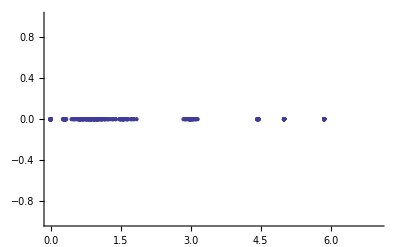

```mathematica
ListPlot[rpoints, PlotRange->{{0, 7}, {-1, 1}},PlotStyle->PointSize[Medium]]
```

```mathematica
xyzpoints=Table[{rtppoints⟦i, 1⟧Sin[rtppoints⟦i, 2⟧]Cos[rtppoints⟦i, 3⟧], rtppoints⟦i, 1⟧Sin[rtppoints⟦i, 2⟧]Sin[rtppoints⟦i, 3⟧], rtppoints⟦i, 1⟧Cos[rtppoints⟦i, 2⟧]}, {i, Length[rtppoints]}];
```

```mathematica
ListPointPlot3D[xyzpoints,
PlotRange->{{-1.5, 1.5}, {-1.5, 1.5}, {-1.5, 1.5}},
PlotStyle->PointSize[Medium],
AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[xyzpoints,
PlotRange->{{-6, 6}, {-6, 6}, {-6, 6}},
PlotStyle->PointSize[Medium],
AxesLabel->{"x","y","z"}]
```

-Graphics3D-

## Testing xi accuracy

```mathematica
f[.5]
```

1.99998

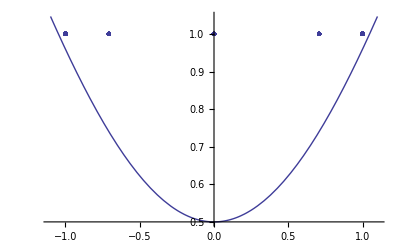

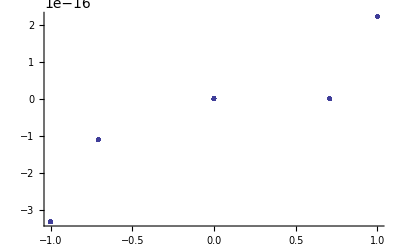

-7.4607×10^-14

2.23821×10^-13

3.33067×10^-16

1.33227×10^-16

-4.44089×10^-17

```mathematica
f[x_]:=1.5x-Sin[x]
(*f[x_]:=Sum[x^n, {n, 0, 16}]*)
fofrpoints=Import["fofr.txt", "Data"];

plot1=Plot[f'[x], {x, -1.1, 1.1}];
plot2=ListPlot[fofrpoints⟦All, {1, 2}⟧, PlotRange->All,PlotStyle->PointSize[Medium]];
Show[plot1, plot2]

ListPlot[fofrpoints⟦All, {1, 3}⟧, PlotRange->All,PlotStyle->PointSize[Medium]]
(*ListPlot[Table[{fofrpoints⟦i, 1⟧, (fofrpoints⟦i, 2⟧+Sin[fofrpoints⟦i, 1⟧])}, {i, Length[fofrpoints]}], PlotRange->All]*)

Total[fofrpoints⟦All, 3⟧]
Total[Abs[fofrpoints⟦All, 3⟧]]
Max[Abs[fofrpoints⟦All, 3⟧]]
Mean[Abs[fofrpoints⟦All, 3⟧]]
Mean[fofrpoints⟦All, 3⟧]
```

## Testing radial derivative accuracy

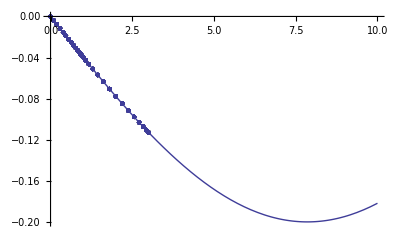

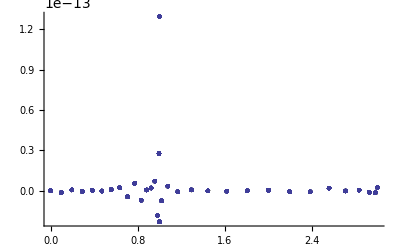

9.89169×10^-12

2.13395×10^-11

1.29584×10^-13

7.47181×10^-15

3.46348×10^-15

```mathematica
fofrpoints=Import["fofr.txt", "Data"];

plot1=Plot[-0.2*Sin[0.2*r], {r, 0, 10}];
plot2=ListPlot[fofrpoints⟦All, {1, 2}⟧, PlotRange->All,PlotStyle->PointSize[Medium]];
Show[plot1, plot2]

ListPlot[fofrpoints⟦All, {1, 3}⟧, PlotRange->All,PlotStyle->PointSize[Medium]]
(*ListPlot[Table[{fofrpoints⟦i, 1⟧, (fofrpoints⟦i, 2⟧+Sin[fofrpoints⟦i, 1⟧])}, {i, Length[fofrpoints]}], PlotRange->All]*)

Total[fofrpoints⟦All, 3⟧]
Total[Abs[fofrpoints⟦All, 3⟧]]
Max[Abs[fofrpoints⟦All, 3⟧]]
Mean[Abs[fofrpoints⟦All, 3⟧]]
Mean[fofrpoints⟦All, 3⟧]
```

```mathematica
Norm[fofrpoints⟦All, 3⟧, 1]
```

1.00883×10^-11

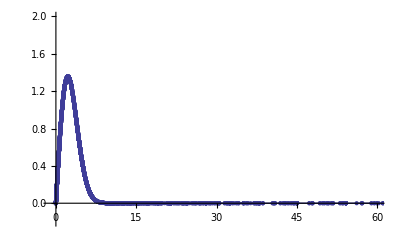

```mathematica
fofrbyrpoints=Import["fofr.txt", "Data"];
plot1=Plot[r ⅇ^(-.1r^2), {r, 0, 60}, PlotRange->{{-1, 60}, {-.2, 2}}];
plot2=ListPlot[fofrbyrpoints, PlotRange->{{-1, 60}, {-.2, 2}},PlotStyle->PointSize[Medium]];
Show[plot1, plot2]
```

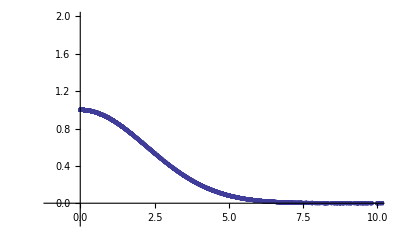

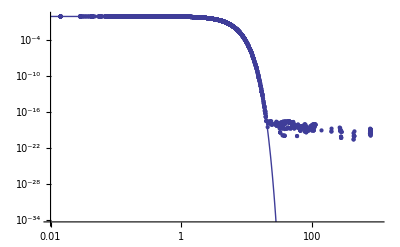

```mathematica
fofrbyrpoints=Import["fofrbyr.txt", "Data"];
plot1=Plot[ⅇ^(-.1r^2), {r, 0, 10}, PlotRange->{{-1, 10}, {-.2, 2}}];
plot2=ListPlot[fofrbyrpoints, PlotRange->{{-1, 10}, {-.2, 2}},PlotStyle->PointSize[Medium]];
Show[plot1, plot2]
plot1=LogLogPlot[ⅇ^(-.1r^2), {r, 1*^-2, 1000}];
plot2=ListLogLogPlot[fofrbyrpoints,PlotStyle->PointSize[Medium]];
Show[plot1, plot2]
```

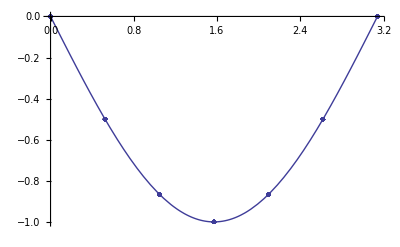

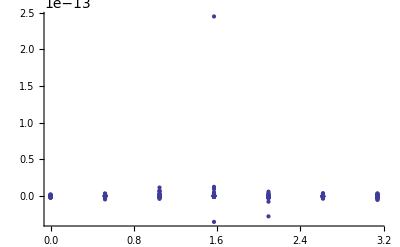

```mathematica
onebyrdfdtpoints=Import["onebyrdfdtheta.txt", "Data"];
plot1=Plot[-Sin[θ], {θ, 0, π}];
plot2=ListPlot[onebyrdfdtpoints, PlotRange->All,PlotStyle->PointSize[Medium]];
Show[plot1, plot2]

ListPlot[Table[{onebyrdfdtpoints⟦i, 1⟧, (onebyrdfdtpoints⟦i, 2⟧+Sin[onebyrdfdtpoints⟦i, 1⟧])}, {i, Length[onebyrdfdtpoints]}], PlotRange->All,PlotStyle->PointSize[Medium]]
```

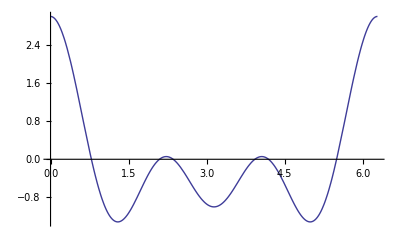

```mathematica
Plot[Cos[θ]+Cos[2θ]+Cos[3θ], {θ, 0, 2π}]
```

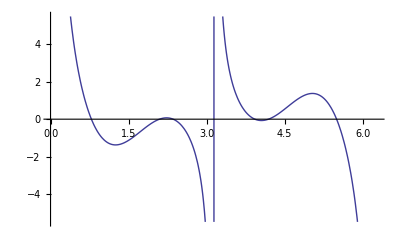

```mathematica
Plot[(Cos[θ]+Cos[2θ]+Cos[3θ])/Sin[θ], {θ, 0, 2π}]
```

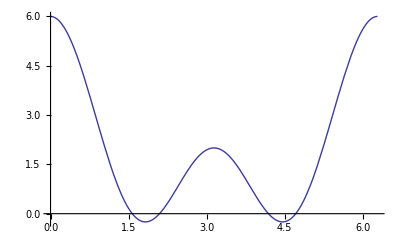

```mathematica
Plot[(Sin[θ]+Sin[2θ]+Sin[3θ])/Sin[θ], {θ, 0, 2π}]
```

```mathematica
Plot[1+, {θ, 0, 2π}]
```

```mathematica
Simplify[(Sin[θ]+Sin[2θ]+Sin[3θ])/Sin[θ]]
```

2 (1+Cos[θ]+Cos[2 θ])

```mathematica
TrigReduce[Sin[θ]^2 Cos[θ]]
```

1/4 (Cos[θ]-Cos[3 θ])

```mathematica
np=20;
phitable=N[Table[2π k/np, {k, 0, np-1}]]
```

{0.,0.314159,0.628319,0.942478,1.25664,1.5708,1.88496,2.19911,2.51327,2.82743,3.14159,3.45575,3.76991,4.08407,4.39823,4.71239,5.02655,5.34071,5.65487,5.96903}

```mathematica
(*B[θ_, ϕ_]:=10SphericalHarmonicY[0,0,θ,ϕ]+1SphericalHarmonicY[1,0,θ,ϕ]+2Im[SphericalHarmonicY[2,1,θ,ϕ]]*)
B0[θ_, ϕ_]:=1(1+.3Sin[θ](Cos[ϕ]+Sin[ϕ])+.2(1-Cos[2θ])(Cos[2ϕ]+Sin[2ϕ]))
SphericalPlot3D[B0[θ, ϕ], {θ,0,Pi},{ϕ,0,2Pi}, MaxRecursion->1]
```

-Graphics3D-

```mathematica
(*B[θ_, ϕ_]:=10SphericalHarmonicY[0,0,θ,ϕ]+1SphericalHarmonicY[1,0,θ,ϕ]+2Im[SphericalHarmonicY[2,1,θ,ϕ]]*)
B1[θ_, ϕ_]:=5(1-.2Sin[θ](Cos[ϕ]+Sin[ϕ])+.1(1-Cos[2θ])(Cos[2ϕ]+Sin[2ϕ]))
SphericalPlot3D[B1[θ, ϕ], {θ,0,Pi},{ϕ,0,2Pi}, MaxRecursion->1]
```

-Graphics3D-

```mathematica
SphericalPlot3D[{B0[θ, ϕ], B1[θ, ϕ]}, {θ,0,Pi},{ϕ,0,2Pi}, MaxRecursion->1]
```

-Graphics3D-

```mathematica
B2[θ_, ϕ_]:=10SphericalHarmonicY[0,0,θ,ϕ]-2Re[SphericalHarmonicY[2,0,θ,ϕ]]+0.5Re[SphericalHarmonicY[4,0,θ,ϕ]]
SphericalPlot3D[B2[θ, ϕ], {θ,0,Pi},{ϕ,0,2Pi}, MaxRecursion->0]
```

-Graphics3D-

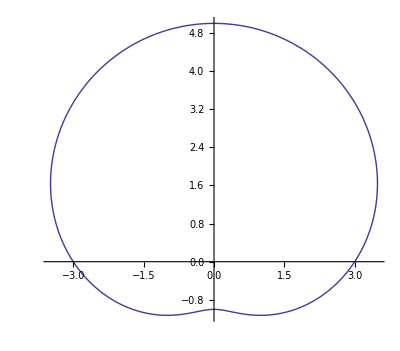

```mathematica
PolarPlot[3+2Cos[θ-π/2], {θ, 0, 2π}]
```

```mathematica
B3[θ_, ϕ_]:=3+2θ ϕ
SphericalPlot3D[B3[θ, ϕ], {θ,0,Pi},{ϕ,0,2Pi}, MaxRecursion->0]
```

-Graphics3D-

```mathematica
B[ArcCos[0.7415311855993943], 4.487989505128276]
```

3.93269

```mathematica
B[ArcCos[xtable⟦1⟧], phitable⟦1⟧]
```

2.35721

```mathematica
Table[B[ArcCos[xtable⟦j⟧], phitable⟦k⟧], {j, 1, nt}, {k, 1, np}]//TableForm
```

2.35721 | 2.71831 | 2.8075 | 2.55761 | 2.15682 | 1.90693 | 1.99611
2.45863 | 3.05962 | 3.20806 | 2.79216 | 2.12511 | 1.70921 | 1.85764
2.62265 | 3.07072 | 3.18139 | 2.87131 | 2.37399 | 2.06391 | 2.17458
2.82095 | 2.82095 | 2.82095 | 2.82095 | 2.82095 | 2.82095 | 2.82095
3.01924 | 2.57117 | 2.46051 | 2.77058 | 3.26791 | 3.57798 | 3.46732
3.18326 | 2.58227 | 2.43384 | 2.84974 | 3.51679 | 3.93269 | 3.78425
3.28468 | 2.92358 | 2.8344 | 3.08429 | 3.48508 | 3.73497 | 3.64578

```mathematica
plot1=SphericalPlot3D[B[θ, ϕ], {θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

```mathematica
plot3=SphericalPlot3D[1, {θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

```mathematica
gridlist=Flatten[Table[{Sin[ArcCos[xtable⟦j⟧]]Cos[phitable⟦k⟧], Sin[ArcCos[xtable⟦j⟧]]Sin[phitable⟦k⟧], Cos[ArcCos[xtable⟦j⟧]]}, {j, 1, nt}, {k, 1, np}], 1];
```

```mathematica
plot4=ListPointPlot3D[gridlist]
```

-Graphics3D-

```mathematica
Show[plot3, plot4]
```

-Graphics3D-

```mathematica
boundlist=Flatten[Table[{B[ArcCos[xtable⟦j⟧], phitable⟦k⟧]Sin[ArcCos[xtable⟦j⟧]]Cos[phitable⟦k⟧], B[ArcCos[xtable⟦j⟧], phitable⟦k⟧]Sin[ArcCos[xtable⟦j⟧]]Sin[phitable⟦k⟧], B[ArcCos[xtable⟦j⟧], phitable⟦k⟧]Cos[ArcCos[xtable⟦j⟧]]}, {j, 1, nt}, {k, 1, np}], 1];
```

```mathematica
plot2=ListPointPlot3D[boundlist]
```

-Graphics3D-

```mathematica
Show[plot1, plot2]
```

-Graphics3D-

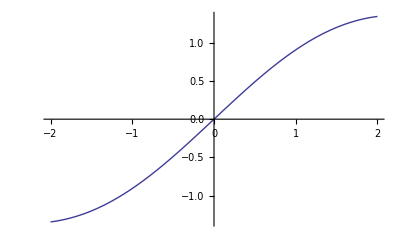

```mathematica
Plot[r*Exp[-0.1*r^2], {r, -2, 2}]
```